```mathematica
1+1
```

2

```mathematica
(* Introduces el modelo, es decir el parámetro de Hubble *)
```

```mathematica
h[z_]=√(om (1+z)^3+1-om)
```

√(1-om+om (1+z)^3)

```mathematica
(* Calculas las otras cantidades *)
```

```mathematica
q[z_]=-1+(1+z) h'[z]/h[z]
```

-1+(3 om (1+z)^3)/(2 (1-om+om (1+z)^3))

```mathematica
r[z_]=(1+z) q'[z]+q [z](1+2 q[z])//Simplify
```

1

```mathematica
(* Asumes valores numéricos para poder graficar las funcciones *)
```

```mathematica
om=0.3
```

0.3

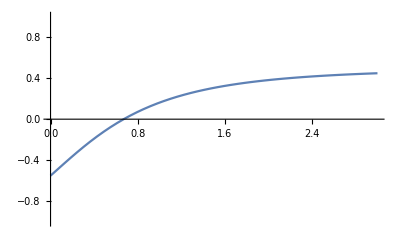

```mathematica
pl1=Plot[q[z],{z,0,3},PlotRange->{-1,1}]
```

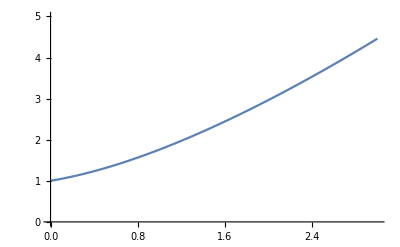

```mathematica
pl2=Plot[h[z],{z,0,3},PlotRange->{0,5}]
```